## DB test?

X gate

```mathematica
err=0.03(*pulse error rate*);
```

```mathematica
σ[n_]:=PauliMatrix[n];
X[ϵ_]:=Cos[π/2(1+ϵ)]σ[0]-I Sin[π/2(1+ϵ)]σ[1];
```

```mathematica
X[0]//MatrixForm
X[0.01]//MatrixForm
```

(0 | -ⅈ
-ⅈ | 0)

(-0.0157073+0. ⅈ | 0.-0.999877 ⅈ
0.-0.999877 ⅈ | -0.0157073+0. ⅈ)

DD Sequence

```mathematica
cycle[n_,ϵ_]:=(X[ϵ].X[ϵ]).cycle[n-1,ϵ];(*doubel X as single cycle, and n is total cycle times*)
cycle[0,ϵ_]:=σ[0];
```

```mathematica
cycle[4,err]
```

{{0.992115+0. ⅈ,0.-0.125333 ⅈ},{0.-0.125333 ⅈ,0.992115+0. ⅈ}}

```mathematica
Table[cycle[n,0]//MatrixForm,{n,0,4}]
```

{(1 | 0
0 | 1),(-1 | 0
0 | -1),(1 | 0
0 | 1),(-1 | 0
0 | -1),(1 | 0
0 | 1)}

```mathematica
fidelity[n_,ϵ_]:=Abs[({{1, 0}}).cycle[n,ϵ].({{1}, {0}})//Tr]^2;(*This is actually the fidelity | ϵ*)
```

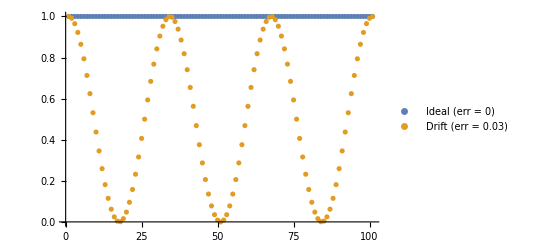

```mathematica
ListPlot[{Table[fidelity[n,0],{n,0,100}],
Table[fidelity[n,err],{n,0,100}]},PlotLegends->{"Ideal (err = 0)","Drift (err = "<>ToString[err]<>")"}]
```